```mathematica
(* 1) run Read data, Construct form functions, Reconstruct solution*)
```

### Read data

```mathematica
SetDirectory[NotebookDirectory[]];
(*SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop-Debug"}]]*)
SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop_Qt_5_10_1_MinGW_32bit-Debug"}]]
```

C:\Users\Darksy\Documents\GitHub\build-RKDG2D-Desktop_Qt_5_10_1_MinGW_32bit-Debug

```mathematica
coeffs =Import["alphaCoeffs/3.000000","Table"];
mesh=Import["mesh2D","Table"];
```

```mathematica
Lx=mesh[[1,3]];
Ly=mesh[[2,3]];
nx=mesh[[3,3]];
ny=mesh[[4,3]];
hx=mesh[[5,3]];
hy=mesh[[6,3]];
numFF=mesh[[7,3]];
MeshCellArea=hx*hy;
MeshCellRcm=mesh[[9;;]];
nCells=Length@MeshCellRcm;
alpha=Table[Partition[coeffs[[i]],numFF],{i,1,nCells}];
```

#### Construct form functions

```mathematica
Phi0[n_,r_]:=1./(√MeshCellArea)
Phi10[n_,r_List]:=√(12./(hy hx^3))(r[[1]]-MeshCellRcm[[n,1]])
Phi11[n_,r_List]:=√(12./(hy^3 hx))(r[[2]]-MeshCellRcm[[n,2]])
Phi20[n_,r_List]:=√(180./(hy hx^5))((r[[1]]-MeshCellRcm[[n,1]])^2-hx^2/12)
Phi21[n_,r_List]:=√(144./(hy^3 hx^3))(r[[1]]-MeshCellRcm[[n,1]])(r[[2]]-MeshCellRcm[[n,2]])
Phi22[n_,r_List]:=√(180./(hy^5 hx))((r[[2]]-MeshCellRcm[[n,2]])^2-hy^2/12)

Phi[n_,r_List]:={Phi0[n,r],Phi10[n,r],Phi11[n,r],Phi20[n,r],Phi21[n,r],Phi22[n,r]}
```

#### Reconstruct solution

```mathematica
GetSol[alpha_,n_,numSol_,r_List]:=Sum[Phi[n,r][[i]]alpha[[n,numSol,i]],{i,numFF}];
```

```mathematica
GetSolDensity[alpha_,n_,numSol_]:=Module[{pts,anSol},(
pts={{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]+hy/2.0},
{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]+hy/2.0}};
anSol=Table[GetSol[alpha,n,numSol,pts[[i]]],{i,1,4}];
Return[Table[{pts[[i,1]],pts[[i,2]],anSol[[i]]},{i,1,4}]]
)];
GetSolGraphics[alpha_,n_,numSol_]:=Module[{pts,anSol},(
pts={{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]+hy/2.0},
{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]+hy/2.0}};
anSol=Table[GetSol[alpha,n,numSol,pts[[i]]],{i,1,4}];
Return[Polygon@Table[{pts[[i,1]],pts[[i,2]],anSol[[i]]},{i,1,4}]]
)];
```

#### Compute integral

```mathematica
(MeshCellRcm[[i]]/.{i->10})-{Lx/2,Ly/2}
GetSol[alpha,i,1,MeshCellRcm[[i]]]/.i->200
```

Part::pkspec1: The expression i cannot be used as a part specification.

{-0.2,-3.8}

Part::pkspec1: The expression i cannot be used as a part specification.

1.

```mathematica
hx hy Sum[GetSol[alpha,i,1,MeshCellRcm[[i]]],{i,1,nCells}]
```

64.

```mathematica
16.0004592
```

16.0005

```mathematica
16.000465920000014 -16.000460079999883
```

5.84×10^-6

```mathematica
16.000460079999883
```

16.0005

```mathematica
16.0004592 -16.000460079999883
```

-8.8×10^-7

```mathematica
16.00156879999998
```

16.0016

#### Draw solution Graphics

```mathematica
Graphics3D[Table[GetSolGraphics[alpha,i,1],{i,1,nCells}]]
```

-Graphics3D-

#### Draw in diag

```mathematica
diagPoints=Table[MeshCellRcm[[i]]-0.5{hx,hy},{i,1,nCells,nx+1}]~Join~{MeshCellRcm[[nCells]]+0.5{hx,hy}};
diagV=diagPoints[[2]]-diagPoints[[1]];
diagH=Norm[diagV,2];
diagX=Table[i*diagH,{i,0,Length[diagPoints]-1}];
diagVal=Table[{GetSol[alpha,i,1,MeshCellRcm[[i]]-0.5{hx,hy}],GetSol[alpha,i,1,MeshCellRcm[[i]]+0.5{hx,hy}]},{i,1,nCells,nx+1}];
```

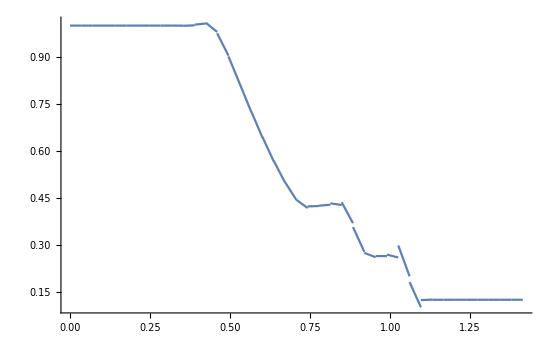

```mathematica
ggg=Show[Table[ListLinePlot[{{diagX[[i]],diagVal[[i,1]]},{diagX[[i+1]],diagVal[[i,2]]}}],{i,1,Length[diagX]-1}],PlotRange->All]
```

Draw in diag cell average

```mathematica
Norm[MeshCellRcm[[1]],2]
```

0.0176777

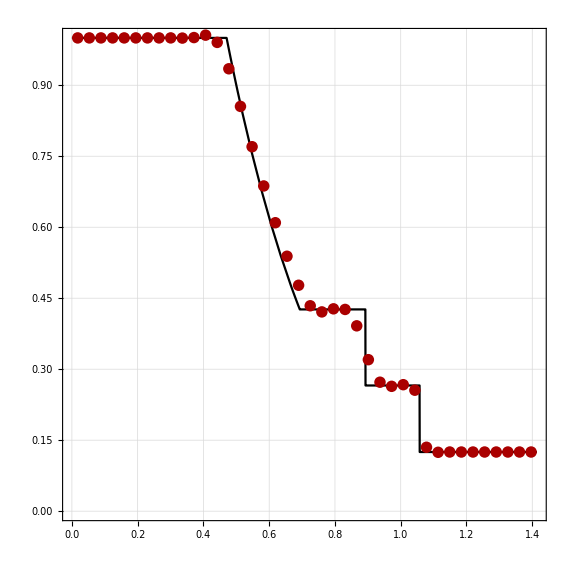

```mathematica
mcc=Table[MeshCellRcm[[i]],{i,1,nCells,nx+1}];
mcy=Table[GetSol[alpha,i,1,MeshCellRcm[[i]]],{i,1,nCells,nx+1}];
mcx=Table[Norm[mcc[[i]],2],{i,Length[mcc]}];
exactDiag=Plot[ρ[x-(√2-1)/2,0.2],{x,0,√2},PlotStyle->Black,Exclusions->None];
grsode=Show[exactDiag,ListPlot[Transpose@{mcx,mcy},
PlotStyle->{Darker[Red],PointSize[0.0145]}],AspectRatio->1,
Frame->True,
FrameStyle->Black,
GridLines->Automatic,
LabelStyle->Directive[12,FontFamily->"Times"]]
```

```mathematica
Export["LLF+WENOS.png",grsode,ImageResolution->300]
```

LLF+WENOS.png

#### Draw in X or Y direction

```mathematica
bou=MeshCellRcm[[All,1]]-hx/2;
```

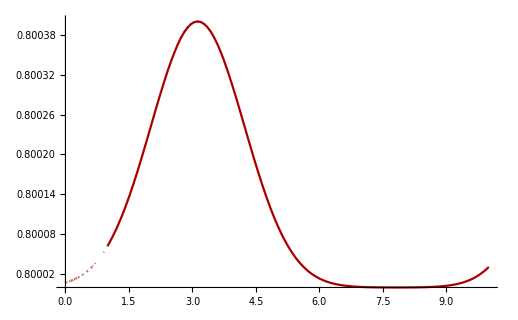

```mathematica
funVis1D[y_]:=Piecewise[Table[{GetSol[alpha,i,1,{0,y}],MeshCellRcm[[i,2]]-hy/2.0 < y <MeshCellRcm[[i,2]]+hy/2.0},{i,1,nCells}]];
funVis1D[x_]:=Piecewise[Table[{(GetSol[alpha,i,1,{x,hy/2}]/1),MeshCellRcm[[i,1]]-hx/2.0 < x <MeshCellRcm[[i,1]]+hx/2.0},{i,1,nx}]];
fig2=Plot[funVis1D[x],{x,0,Lx},Exclusions->bou,PlotPoints->100,PlotRange->All,PlotStyle->Darker[Red]]
```

```mathematica
getPressure[x_,i_]:=(1.4-1)(GetSol[alpha,i,5,{x,(Lx+hx)/2}]-1/2((GetSol[alpha,i,2,{x,(Lx+hx)/2}]^2+GetSol[alpha,i,3,{x,(Lx+hx)/2}]^2+GetSol[alpha,i,4,{x,(Lx+hx)/2}]^2)/GetSol[alpha,i,1,{x,(Lx+hx)/2}]))
```

```mathematica
getEnthalpy[x_,i_]:=(getPressure[x,i]+GetSol[alpha,i,5,{x,(Lx+hx)/2}])/GetSol[alpha,i,1,{x,(Lx+hx)/2}]
```

```mathematica
funVisp1D[x_]:=Piecewise[Table[{(getPressure[x,i]),MeshCellRcm[[i,1]]-hx/2.0 < x <MeshCellRcm[[i,1]]+hx/2.0},{i,nx ny/2+1,nx ny/2+nx}]];
grp=Plot[funVisp1D[x],{x,0,12},Exclusions->bou,PlotPoints->100,PlotRange->All,PlotStyle->Darker[Red]];
```

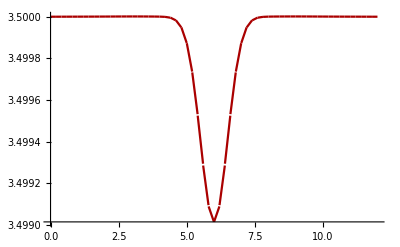

```mathematica
funVish1D[x_]:=Piecewise[Table[{(getEnthalpy[x,i]),MeshCellRcm[[i,1]]-hx/2.0 < x <MeshCellRcm[[i,1]]+hx/2.0},{i,nx ny/2+1,nx ny/2+nx}]];
grh=Plot[funVish1D[x],{x,0,12},Exclusions->bou,PlotPoints->100,PlotRange->All,PlotStyle->Darker[Red]]
```

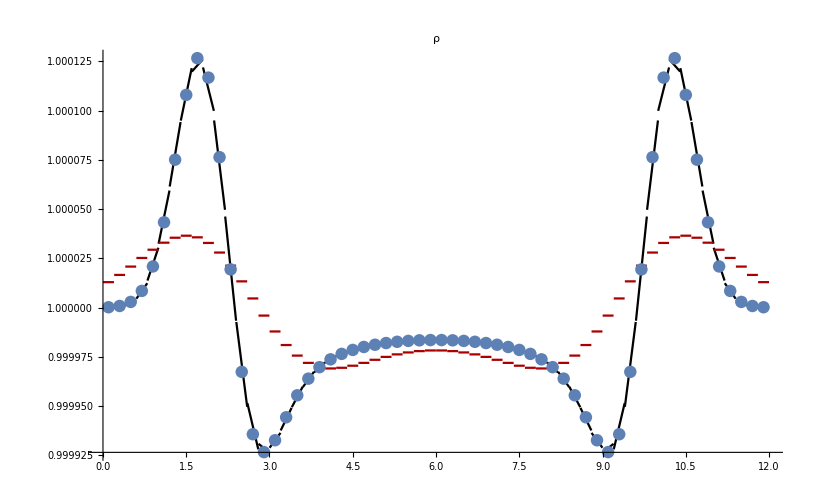

```mathematica
Show[fig1,fig2,ListPlot[dataAnCenterRhoEqP,PlotRange->All],PlotLabel->"ρ",LabelStyle->Directive[{Black,12}],AxesStyle->Black]
```

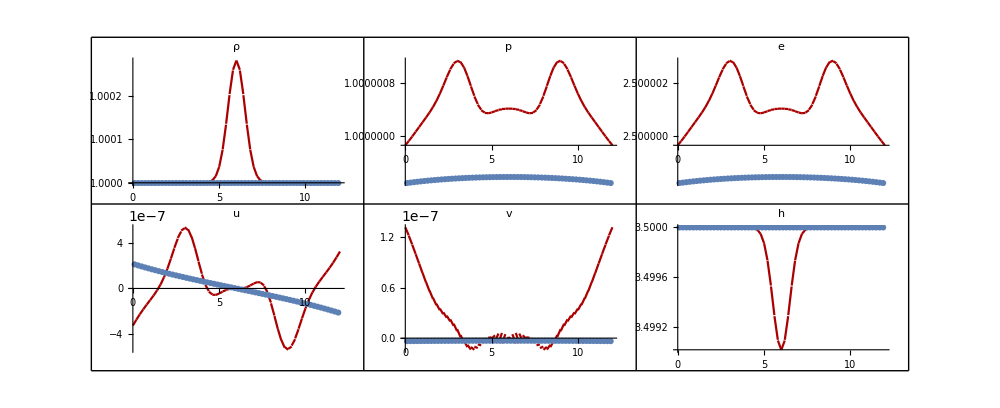

```mathematica
full=GraphicsGrid[{{Show[fig2,ListPlot[dataAnCenterRhoEqP,PlotRange->All],PlotLabel->"ρ",LabelStyle->Directive[{Black,12}],AxesStyle->Black],Show[grp,ListPlot[dataAnCenterRhoEqP,PlotRange->All],PlotLabel->"p",LabelStyle->Directive[{Black,12}],AxesStyle->Black],
Show[fig2e,ListPlot[dataAnCenterE,PlotRange->All],PlotLabel->"e",
LabelStyle->Directive[{Black,12}],AxesStyle->Black]},
{Show[fig2U,ListPlot[dataAnCenterU,PlotRange->All],PlotLabel->"u",
LabelStyle->Directive[{Black,12}],AxesStyle->Black],Show[fig2V,ListPlot[dataAnCenterV,PlotRange->All],PlotLabel->"v",
LabelStyle->Directive[{Black,12}],AxesStyle->Black],
Show[grh,ListPlot[dataAnCenterH,PlotRange->All],PlotLabel->"h",
LabelStyle->Directive[{Black,12}],AxesStyle->Black]}},
Frame->All,ImageSize->1000]
```

```mathematica
Export["t=20.jpg",full,ImageResolution->150]
```

t=20.jpg

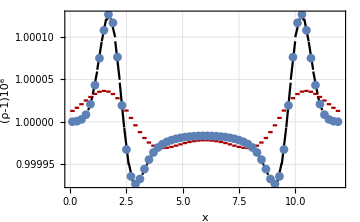

```mathematica
grd=Table[MeshCellRcm[[i,1]]-hx/2,{i,1,nx}]~Join~{MeshCellRcm[[nx,1]]+hx/2};
ee=Show[fig1,fig2,ListPlot[dataAnCenterRhoEqP,PlotRange->All,PlotMarkers->Automatic],
Frame->True,
GridLines->{grd,Automatic},
ImageSize->Medium,
LabelStyle->Directive[Black,12,FontFamily->"Times"],
FrameLabel->{"x","(ρ-1)10^6"}]
```

```mathematica
Export["LF_t=2.png",ee,ImageResolution->300]
```

LF_t=2.png

#### Draw Sode problem

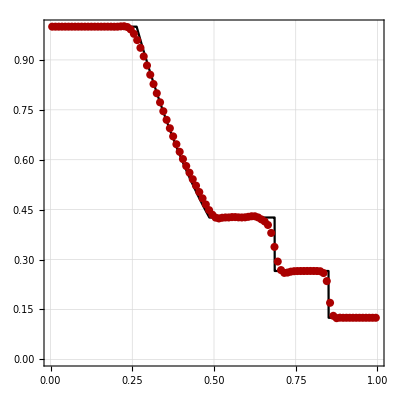

```mathematica
exact=Plot[ρ[x,0.2],{x,0,1},PlotStyle->Black,Exclusions->None];
grsode=Show[exact,ListPlot[Table[{MeshCellRcm[[i,1]],GetSol[alpha,i,1,MeshCellRcm[[i]]]},{i,1,nx}],PlotStyle->{Darker[Red],PointSize[0.0145]}],AspectRatio->1,
Frame->True,
FrameStyle->Black,
GridLines->Automatic,
LabelStyle->Directive[12,FontFamily->"Times"]]
```

```mathematica
grsodeDiag=Show[exact,ListPlot[Table[{MeshCellRcm[[i,1]],GetSol[alpha,i,1,MeshCellRcm[[i]]]},{i,1,nx}],PlotStyle->{Darker[Red],PointSize[0.0145]}],AspectRatio->1,
Frame->True,
FrameStyle->Black,
GridLines->Automatic,
LabelStyle->Directive[12,FontFamily->"Times"]]
```

```mathematica
Export["HLLC+WENOS+Everywhere.png",grsode,ImageResolution->300]
```

HLLC+WENOS+Everywhere.png

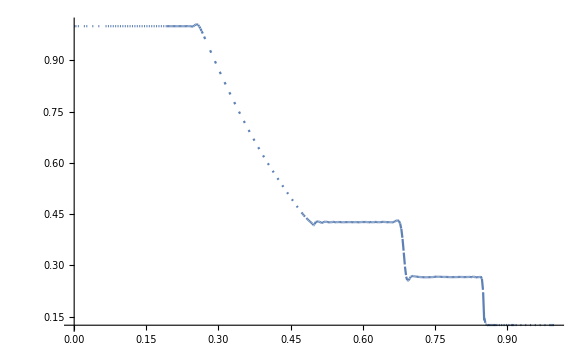

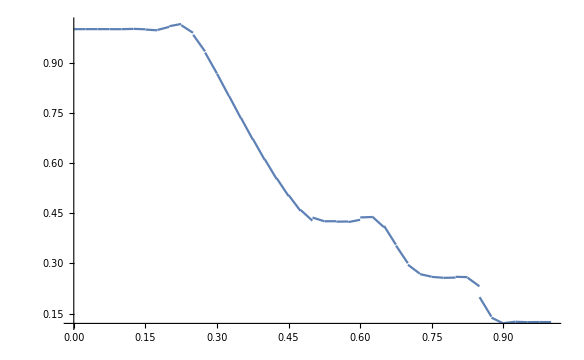

```mathematica
troubledCells={50,51}+1
funVis1DLim[x_]:=Piecewise[Table[{GetSol[alpha,i,1,{x,0}],MeshCellRcm[[i,1]]-hx/2.0 < x <MeshCellRcm[[i,1]]+hx/2.0},{i,troubledCells}]];
```

{51,52}

```mathematica
trb=Plot[funVis1DLim[x],{x,0,1},PlotStyle->Red,Exclusions->bou,PlotPoints->200];
```

Part::partw: Part 51 of {{0.0125,0.25},{0.0375,0.25},{0.0625,0.25},{0.0875,0.25},{0.1125,0.25},{0.1375,0.25},{0.1625,0.25},{0.1875,0.25},{0.2125,0.25},{0.2375,0.25},{0.2625,0.25},{0.2875,0.25},«16»,{0.7125,0.25},{0.7375,0.25},{0.7625,0.25},{0.7875,0.25},{0.8125,0.25},{0.8375,0.25},{0.8625,0.25},{0.8875,0.25},{0.9125,0.25},{0.9375,0.25},{0.9625,0.25},{0.9875,0.25}} does not exist.

Part::partw: Part 51 of {{{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan}},{{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan}},«37»,{{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Show[fig,trb]
```

-Graphics-

#### Draw density plot

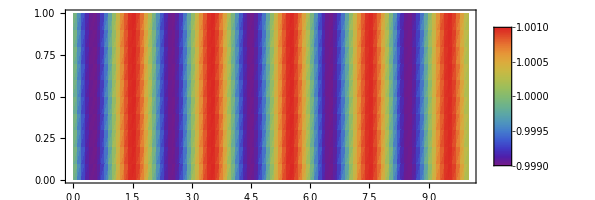

```mathematica
ListDensityPlot[Table[GetSolDensity[alpha,i,1],{i,1,nCells}],AspectRatio->Automatic,PlotRange->All,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```